```mathematica
alluvk=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/3 IA Fluorimeter and UVVis/140521 UVVis/uvvis kinetics.csv"];

importuvk[kinfile_]:=
Module[{datacolumn,name,time,abs,listname,templist,wavelength,varname,min},
datacolumn=3;(*the desired data starts here*)
listname=ToExpression[StringJoin["list",ToString[Unevaluated[kinfile]]]];
(*creates name of list of lists as list"inputfilename"*)
templist={};
(*makes templist an empty list to which names can be added*)
While[datacolumn≤Length[kinfile[[1]]](*continues while datacolumn index is ≤ width of spectra*),
name=ToExpression[Evaluate[kinfile[[5,datacolumn]]]];(*converts desired name from string to symbol*)
If[Head[name]===List,(*if name is already a list, skip it, increment datacolumn, and move on, if not, then do everything*)
++datacolumn;
++datacolumn,
templist=Insert[templist,ToString[name],-1];
(*adds name of current file to the list*)
time=kinfile[[17;;-1,datacolumn-1]];
(*selects only data not header rows for the time values*)
abs=kinfile[[17;;-1,datacolumn]];(*these are the absorbance values for the current set of data*)
wavelength=kinfile[[3,datacolumn]];
(*this are the wavelength used for the kinetics experiment*)
varname=kinfile[[5,datacolumn]];
(*this stores the file name to make processing later easier*)
min=kinfile[[14,datacolumn]];
(*the lowerbound for graphing*)
time=DeleteCases[time,""];(*deletes blank items*)
abs=DeleteCases[abs,""];
Evaluate[name]={Evaluate[{time,abs}ᵀ],min,wavelength,varname};
(*saves data with name (which must be evaluated so they won't all be called "name") and is transposed so that they end up in columns correctly, followed by the wavelength and desired filename at the bottom*)
++datacolumn;
++datacolumn;
Clear[wavelength,varname,time,abs](*clear these variables for next time*)]
(*increments column by 2 to get to the next set of data two columns over*)];
If[Head[listname]===List,
AppendTo[listname,templist],
Evaluate[listname]=templist
(*sets listname to value of templist which is list of strings of the names of the lists created in the while loop*)]]
SetAttributes[importuvk,HoldAllComplete]

exportPDFuvk[kinname_]:=(*this takes a single argument that is a string of the name of the kinetics variable to be exported with name "kinname.pdf"*)Export[StringJoin[{kinname,".pdf"}](*name is the name of the file (already a string).pdf, which automatically sets the file format*),
makeuvkPlot[ToExpression[kinname]]]
(*SetAttributes[ExportPDFSpectrum,HoldFirst]*)

makeuvkPlot[kin_]:=Module[{data,ylabel,wavelength,ticks,ticksmajor,ticksminor,ticksminorloc,min},
data=kin[[1]](*this range excludes wavelength and name listed at the end*);
min=kin[[-3]];(*lower bound for graph*)
wavelength=kin[[-2]];(*wavelength used for this experiment for labeling*)
ticks=FindDivisions[{data[[1,1]],data[[-1,1]]},6];
ticksmajor=FindDivisions[{data[[1,1]],data[[-1,1]]},6];
ticksminorloc=Complement[FindDivisions[{data[[1,1]],data[[-1,1]]},30],FindDivisions[{data[[1,1]],data[[-1,1]]},6]];
ticksminor={};
Do[AppendTo[ticksminor,Evaluate[Join[{ticksminorloc[[i]]},{"",{.006,0}}]]],{i,Length[ticksminorloc]}];
ticks=Join[ticksmajor,ticksminor];
(*manually defines x ticks because they weren't fitting with the enlarged font size*)
ylabel=StringJoin["λ: ",ToString[wavelength]," nm","\nabsorbance"];
ListPlot[data,PlotStyle->Black,AxesOrigin->{data[[1,1]],0},Joined->True,Filling->Axis,FillingStyle->LightGray,PlotRange->{{data[[1,1]],data[[-1,1]]},{min,All}},Frame->True,FrameLabel->{{ylabel,""},{"time (s)",""}},LabelStyle->18,FrameTicks->{{Automatic,None},{ticks,None}},FrameStyle->16]]

exportuvk[kinlist_]:=Module[{index},
index=0;
While[index<Dimensions[kinlist][[1]],
index++;
exportPDFuvk[kinlist[[index]]];
Print[index]]]
```

```mathematica
Quit[]
```

```mathematica
importuvk[alluvk]
```

{uvkbufferpshort,uvkaminep,uvkinsulinplate,uvkinsulinp,uvkbufferp315,uvkbufferp340,uvkbufferpcomb}

```mathematica
exportuvk[listalluvk]
```

1

2

3

4

5

6

7

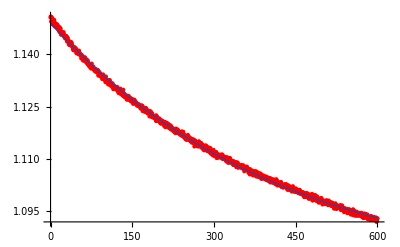

{kH→0.00235364,a→1.17282,b→1.07508,t0→-118.993}

uvkbufferpshort

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

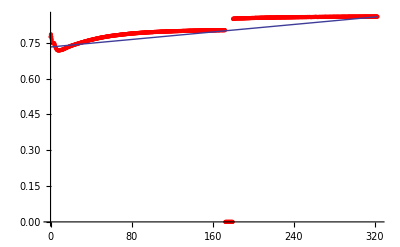

{kH→4.55754×10^-6,a→0.763633,b→86.9023,t0→80.2889}

uvkaminep

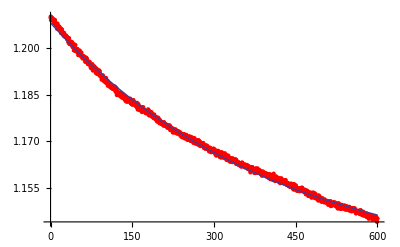

{kH→0.00244961,a→1.28738,b→1.12758,t0→-279.13}

uvkinsulinplate

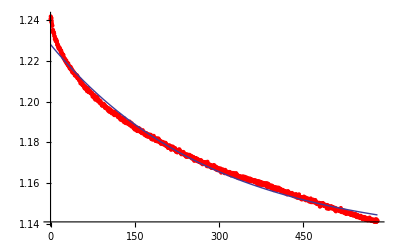

{kH→0.00348942,a→1.27675,b→1.13177,t0→-117.306}

uvkinsulinp

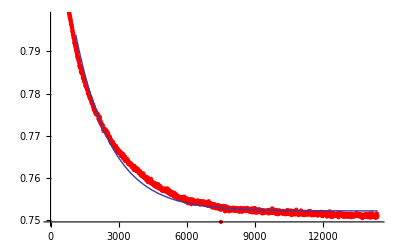

{kH→0.000634543,a→0.914269,b→0.752196,t0→-1026.81}

uvkbufferp315

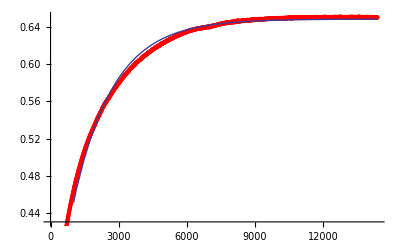

{kH→0.000569475,a→0.106328,b→0.648403,t0→-771.17}

uvkbufferp340

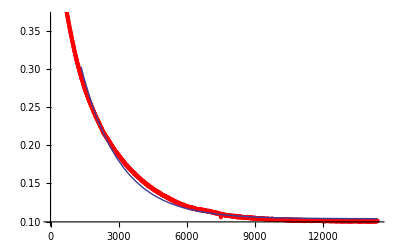

{kH→0.000580896,a→0.459118,b→0.103814,t0→342.821}

uvkbufferpcomb

```mathematica
fitModelstoDataList[listalluvk]
```